## One parameter

```mathematica
u1[θ1_,γ_]:=a1 θ1^4+ b1 θ1^3+(c1) θ1^2+γ d1 θ1
u2[θ2_,γ_]:=a2 θ2^4+ b2 θ2^3+(c2 )θ2^2+γ d2 θ2
u12[θ1_,θ2_,k12_]:=k12/2*(θ1-θ2)^2
u21[θ1_,θ2_,k12_]:=k12/2*(θ2-θ1)^2
Energy[θ1_,θ2_,γ_,k12_]:=u1[θ1,γ]+u2[θ2,γ]+1/2 u12[θ1,θ2,k12]+1/2 u21[θ1,θ2,k12]
F[θ1_,θ2_,γ_,k12_]:={D[Energy[θ11,θ22,γ,k12],θ11],D[Energy[θ11,θ22,γ,k12],θ22]}/.{θ11->θ1,θ22->θ2}
```

```mathematica
a1=2.2;a2=2;b1=1;b2=1;c1=-5;c2=-4;d1=-1;d2=-1;
```

```mathematica
bifurcationpoints[k12_]:={θ1,θ2,γ}/.NSolve[{-D[Energy[θ1,θ2,γ,k12],θ1]==0,-D[Energy[θ1,θ2,γ,k12],θ2]==0,(D[D[Energy[θ1,θ2,γ,k12],θ1],θ1]*D[D[Energy[θ1,θ2,γ,k12],θ2],θ2])-(D[D[Energy[θ1,θ2,γ,k12],θ1],θ2]*D[D[Energy[θ1,θ2,γ,k12],θ2],θ1])==0},{θ1,θ2,γ},Reals]
branchpoints={θ1,θ2,γ,k12}/.NSolve[{-D[Energy[θ1,θ2,γ,k12],θ1]==0,-D[Energy[θ1,θ2,γ,k12],θ2]==0,-D[D[Energy[θ1,θ2,γ,k12],θ1],θ1]==-1.05*D[D[Energy[θ1,θ2,γ,k12],θ1],θ2],-1.05*D[D[Energy[θ1,θ2,γ,k12],θ2],θ2]==-D[D[Energy[θ1,θ2,γ,k12],θ1],θ2]},{θ1,θ2,γ,k12},Reals]
```

{{-1.569,-1.59386,-11.4676,-22.2326},{1.57599,1.58654,26.4722,-31.7202}}

```mathematica
Jacob[θ1_,θ2_,γ_,k12_]:={{-D[D[Energy[θ11,θ2,γ,k12],θ11],θ11]/.{θ11->θ1,θ22->θ2},-D[D[Energy[θ11,θ22,γ,k12],θ11],θ22]/.{θ11->θ1,θ22->θ2}},{-D[D[Energy[θ11,θ22,γ,k12],θ11],θ22]/.{θ11->θ1,θ22->θ2},-D[D[Energy[θ11,θ22,γ,k12],θ22],θ22]/.{θ11->θ1,θ22->θ2}}}
```

```mathematica
eigensys[n_,k12_]:=Chop@SortBy[Eigensystem[Jacob[bifurcationpoints[k12][[n,1]],bifurcationpoints[k12][[n,2]],bifurcationpoints[k12][[n,3]],k12]],Abs[#[[1]]]&]
Fγ:=D[F[θ1,θ2,γ1,k12],γ1]/.γ1->γ
condition1[n_,k12_]:=eigensys[n,k12][[2,2]].Fγ
condition2[n_,k12_]:=eigensys[n,k12][[2,2]].{6+48 *bifurcationpoints[k12][[n,1]]*(eigensys[n,k12][[2,2,1]])^2,6+52.8 *bifurcationpoints[k12][[n,2]]*(eigensys[n,k12][[2,2,2]])^2}
```

```mathematica
D[D[F[θ1,θ2,γ,k12][[1]],θ1],θ1]
```

6+48 θ1

```mathematica
Clear[n];Clear[k];f[n_,k_]:={condition2[n,k],bifurcationpoints[k][[n,1]],bifurcationpoints[k][[n,2]],bifurcationpoints[k][[n,3]],eigensys[n,k][[1,1]]}
```

```mathematica
ftable=Table[Table[f[n,k],{n,1,Length@bifurcationpoints[k]}],{k,.84,.8405,.00002}];
```

```mathematica
ktbl=Table[x,{x,.84,.8405,.00002}];
points[kindex_]:={#[[4]],ktbl[[kindex]]}&/@ftable[[kindex]]
sz=10;
colors[kindex_]:=Which[#[[1]]<0&&#[[2]]<-.01&&#[[3]]<-.01&&#[[5]]<0,Black,#[[1]]<0&&#[[2]]>.01&&#[[3]]<-.01&&#[[5]]<0,Red,#[[1]]<0&&#[[2]]<-.01&&#[[3]]>.01&&#[[5]]<0,Blue,#[[1]]<0&&#[[2]]>.01&&#[[3]]>.01&&#[[5]]<0,Magenta,#[[1]]>0&&#[[2]]<-.01&&#[[3]]<-.01&&#[[5]]<0,Black,#[[1]]>0&&#[[2]]>.1&&#[[3]]<-.01&&#[[5]]<0,Red,#[[1]]>0&&#[[2]]<-.01&&#[[3]]>.01&&#[[5]]<0,Blue,#[[1]]>0&&#[[2]]>.01&&#[[3]]>.01&&#[[5]]<0,Magenta,#[[5]]>0,Green]&/@ftable[[kindex]]
shapes[kindex_]:=Which[#[[1]]<0&&#[[2]]<-.001&&#[[3]]<-.001,{"■",sz},#[[1]]<0&&#[[2]]>.01&&#[[3]]<-.01,{"■",sz},#[[1]]<0&&#[[2]]<-.001&&#[[3]]>.001,{"■",sz},#[[1]]<0&&#[[2]]>.001&&#[[3]]>.001,{"■",sz},#[[1]]>0&&#[[2]]<-.01&&#[[3]]<-.001,{"●",sz},#[[1]]>0&&#[[2]]>.001&&#[[3]]<-.001,{"●",sz},#[[1]]>0&&#[[2]]<-.001&&#[[3]]>.001,{"●",sz},#[[1]]>0&&#[[2]]>.01&&#[[3]]>.001,{"●",sz}]&/@ftable[[kindex]]
```

```mathematica
Length@ktbl
```

26

```mathematica
a={#[[3]],#[[4]]}&/@ss
```

{{4.41129,4.22337},{2.20532,3.91877},{1.50682,3.85962},{0.663863,3.53675},{-2.42137,3.27784},{0.0752164,3.58075}}

```mathematica
sss=Table[points[i],{i,1,Length@ktbl}]
```

{{{2.66961,0.83},{3.80549,0.83},{4.37065,0.83},{4.39024,0.83},{-0.757487,0.83},{-1.99613,0.83},{-2.42616,0.83},{-1.87005,0.83}},{{2.66191,0.835},{3.80372,0.835},{4.3723,0.835},{4.38224,0.835},{-0.749518,0.835},{-1.99476,0.835},{-2.42734,0.835},{-1.86232,0.835}},{{2.65423,0.84},{3.80194,0.84},{4.37393,0.84},{4.37424,0.84},{-0.741557,0.84},{-1.99338,0.84},{-2.42851,0.84},{-1.85461,0.84}},{{2.64655,0.845},{3.80016,0.845},{4.37557,0.845},{4.36626,0.845},{-0.733604,0.845},{-1.992,0.845},{-2.42969,0.845},{-1.8469,0.845}},{{2.63889,0.85},{3.79838,0.85},{4.3772,0.85},{4.35828,0.85},{-0.72566,0.85},{-1.99062,0.85},{-2.43086,0.85},{-1.8392,0.85}}}

```mathematica
condition2[8,.84]
```

-30.4774

```mathematica
sss[[-4]]
```

{{2.65423,0.84},{3.80194,0.84},{4.37393,0.84},{4.37424,0.84},{-0.741557,0.84},{-1.99338,0.84},{-2.42851,0.84},{-1.85461,0.84}}

```mathematica
condition2[]
```

```mathematica
Show[ParametricPlot[{x,.84015},{x,4.3,4.5}],Table[ListPlot[List/@points[i],PlotStyle->colors[i],PlotMarkers->shapes[i]],{i,1,Length@ktbl}],PlotRange->{{4.372,4.376},{.83,.85}}]
```

```mathematica
Clear[k12]
```

```mathematica
k12=1;
```

```mathematica
vec1[θ1_, θ2_, d_] := FullSimplify[D[Energy[θ1,θ2, d], 
     {{θ1,θ2}}]]; 
vc1[d_?NumericQ]:=θ1/. NSolve[vec1[θ1,θ2, d]==0,{θ1,θ2},Reals];
vc2[d_?NumericQ]:=θ2/. NSolve[vec1[θ1,θ2, d]==0,{θ1,θ2},Reals];
spliceThread=Splice@*Thread;
coords1=Table[spliceThread[{vc1[d],vc2[d],d}],{d,-12,12,.02}];
coords={#[[1]],#[[2]]}&/@coords1;
hessian=(D[Energy[x22,x33, y], {{x22,x33}},{{x22,x33}}]/.{x22->#[[1]],x33->#[[2]]})&/@coords;
eigenvals=Table[Eigenvalues[hessian[[i]]],{i,1,Length@hessian,1}];
vertexColors1=Which[#[[1]]>0&&#[[2]]>0,RGBColor[.94,.31,.22],#[[1]]>0&&#[[2]]<0,Magenta,#[[1]]<0&&#[[2]]>0,Magenta,#[[1]]<0&&#[[2]]<0,RGBColor[.122,.267,.62],Chop[#[[1]]]==0||Chop[#[[2]]]==0,Yellow]&/@eigenvals;
```

```mathematica
Show[ContourPlot3D[z==bifurcationpoints[[3,3]]+.1,{x,-2,2},{y,-2,2},{z,-10,10}],(*ContourPlot3D[{x==θ1m,y==θ1m,x==θ1p,y==θ2p},{x,-2,2},{y,-2,2},{z,-15,15}],*)ListPointPlot3D[List/@coords1,PlotStyle->vertexColors1],AxesLabel->{"θ1","θ2","γ"},LabelStyle->Directive[Bold, Medium],PlotRange->All]
```

## Solving for the dynamics

```mathematica
u1[θ1_,γ_]:=a1 θ1^4+ b1 θ1^3+(c1) θ1^2+γ d1 θ1
u2[θ2_,γ_]:=a2 θ2^4+ b2 θ2^3+(c2 )θ2^2+γ d2 θ2
u12[θ1_,θ2_,k12_]:=k12/2*(θ1-θ2)^2
u21[θ1_,θ2_,k12_]:=k12/2*(θ2-θ1)^2
Energy[θ1_,θ2_,γ_,k12_]:=u1[θ1,γ]+u2[θ2,γ]+1/2 u12[θ1,θ2,k12]+1/2 u21[θ1,θ2,k12]
F[θ1_,θ2_,γ_,k12_]:={D[Energy[θ11,θ22,γ,k12],θ11],D[Energy[θ11,θ22,γ,k12],θ22]}/.{θ11->θ1,θ22->θ2}
a1=2;a2=2.2;b1=1;b2=1;c1=-5;c2=-4;d1=-1;d2=-1;
eqn1=(F[θ1,θ2,γ,k12][[1]]/.{θ1->θ1[t],θ2->θ2[t]});
eqn2=(F[θ1,θ2,γ,k12][[2]]/.{θ1->θ1[t],θ2->θ2[t]});
```

```mathematica
sol=ParametricNDSolve[{θ1'[t]==-eqn1,θ2'[t]==-eqn2,θ1[0]==a,θ2[0]==0},{θ1,θ2},{t,0,100},{a,b,γ,k12}]
theta1[a_,b_,γ_,k12_,t_]:=θ1[a,b,γ,k12][t]/.sol
theta2[a_,b_,γ_,k12_,t_]:=θ2[a,b,γ,k12][t]/.sol
```

{θ1→ParametricFunction[<>],θ2→ParametricFunction[<>]}

```mathematica
aa=SortBy[bifurcationpoints[-1],#[[3]]&]
```

{{0.564321,-1.40333,-5.21779},{-1.52621,0.482083,-4.18181},{0.302234,0.476623,-2.35305},{0.848078,0.483992,-1.80741},{-1.16047,-0.710679,3.59217},{-0.468438,-0.704728,4.28406},{1.25451,-0.709394,6.00722},{-0.814285,1.19758,7.82453}}

```mathematica
theta1[aa[[5,1]],aa[[5,2]],aa[[5,3]],-1,100]
theta2[aa[[5,1]],aa[[5,2]],aa[[5,3]],-1,100]
```

-1.26545

1.07975

```mathematica
(eqn2/.{γ->aa[[5,3]],k12->-1})
```

-3.59217+θ1[t]-9 θ2[t]+3 θ2[t]^2+8.8 θ2[t]^3

```mathematica
{θ1[t],θ2[t]}/.NSolve[{(eqn1/.{γ->aa[[5,3]],k12->-1}),(eqn2/.{γ->aa[[5,3]],k12->-1})}==0,{θ1[t],θ2[t]},Reals]
{θ1[t],θ2[t]}/.NSolve[{(eqn1/.{γ->aa[[5,3]]+.001,k12->-1}),(eqn2/.{γ->aa[[5,3]]+.001,k12->-1})}==0,{θ1[t],θ2[t]},Reals]
```

{{1.11703,0.985867},{-1.16047,-0.710679},{-1.16047,-0.710679},{-0.414688,-0.9148},{1.16327,-0.264655},{-0.368352,-0.46692},{-1.26545,1.07975},{1.19048,-1.06196},{-0.226354,1.04135}}

{{1.11707,0.98591},{-0.41478,-0.914657},{1.16331,-0.264765},{-0.368471,-0.467105},{-1.2654,1.07978},{1.19051,-1.0619},{-0.22644,1.04139}}

```mathematica
Eigenvalues[({{-D[F[θ1,θ2,γ,k12][[1]],θ1],-D[F[θ1,θ2,γ,k12][[1]],θ2]},{-D[F[θ1,θ2,γ,k12][[1]],θ2],-D[F[θ1,θ2,γ,k12][[2]],θ2]}})/.{θ1->theta1[aa[[5,1]],aa[[5,2]],aa[[5,3]]+0.001,-1,100],θ2->theta2[aa[[5,1]],aa[[5,2]],aa[[5,3]]+0.001,-1,100],γ->aa[[5,3]]+0.001,k12->-1}]
```

{10.1932,5.80157}

## Two parameters

```mathematica
u1[θ1_,a1_,γ_]:=c1 θ1^4+ b1 θ1^3+(a1) θ1^2+γ d1 θ1
u2[θ2_,γ_]:=a2 θ2^4+ b2 θ2^3+(c2 )θ2^2+γ d2 θ2
u12[θ1_,θ2_,k12_]:=k12/2*(θ1-θ2)^2
u21[θ1_,θ2_,k12_]:=k12/2*(θ2-θ1)^2
Energy[θ1_,θ2_,γ_,k12_,a1_]:=u1[θ1,a1,γ]+u2[θ2,γ]+1/2 u12[θ1,θ2,k12]+1/2 u21[θ1,θ2,k12]
F[θ1_,θ2_,γ_,k12_,a1_]:={D[Energy[θ11,θ22,γ,k12,a1],θ11],D[Energy[θ11,θ22,γ,k12,a1],θ22]}/.{θ11->θ1,θ22->θ2}
```

```mathematica
c1=2;a2=2;b1=1;b2=1;Clear[a1];c2=-4;d1=-1;d2=-1;
```

```mathematica
bifurcationpoints[k12_,a1_]:={θ1,θ2,γ}/.NSolve[{-D[Energy[θ1,θ2,γ,k12,a1],θ1]==0,-D[Energy[θ1,θ2,γ,k12,a1],θ2]==0,(D[D[Energy[θ1,θ2,γ,k12,a1],θ1],θ1]*D[D[Energy[θ1,θ2,γ,k12,a1],θ2],θ2])-(D[D[Energy[θ1,θ2,γ,k12,a1],θ1],θ2]*D[D[Energy[θ1,θ2,γ,k12,a1],θ2],θ1])==0},{θ1,θ2,γ},Reals]
```

```mathematica
bifurcationpoints[2,-5]
```

{{-0.940268,-0.661304,4.8467},{-0.27795,-0.619262,3.5221},{0.83029,-0.652206,1.30933},{0.633904,0.419261,-2.66645},{0.121273,0.366465,-1.64473},{-0.725492,0.803763,2.72059},{0.476548,-1.0216,-0.222115},{-1.11123,0.401079,0.814732}}

```mathematica
Jacob[θ1_,θ2_,γ_,k12_,a1_]:={{-D[D[Energy[θ11,θ2,γ,k12,a1],θ11],θ11]/.{θ11->θ1,θ22->θ2},-D[D[Energy[θ11,θ22,γ,k12,a1],θ11],θ22]/.{θ11->θ1,θ22->θ2}},{-D[D[Energy[θ11,θ22,γ,k12,a1],θ11],θ22]/.{θ11->θ1,θ22->θ2},-D[D[Energy[θ11,θ22,γ,k12,a1],θ22],θ22]/.{θ11->θ1,θ22->θ2}}}
```

```mathematica
eigensys[n_,k12_,a1_]:=Chop@SortBy[Eigensystem[Jacob[bifurcationpoints[k12,a1][[n,1]],bifurcationpoints[k12,a1][[n,2]],bifurcationpoints[k12,a1][[n,3]],k12,a1]],Abs[#[[1]]]&]
Fγ:=D[F[θ1,θ2,γ1,k12,a1],γ1]/.γ1->γ
condition1[n_,k12_,a1_]:=eigensys[n,k12,a1][[2,2]].Fγ
condition2[n_,k12_,a1_]:=eigensys[n,k12,a1][[2,2]].{(D[D[F[θ11,θ2,γ,k12,a1][[1]],θ11],θ11]/.{θ11->bifurcationpoints[k12,a1][[n,1]]})*(eigensys[n,k12,a1][[2,2,1]])^2,(D[D[F[θ1,θ22,γ,k12,a1][[2]],θ22],θ22]/.{θ22->bifurcationpoints[k12,a1][[n,2]]})*(eigensys[n,k12,a1][[2,2,2]])^2}
```

```mathematica
Clear[n];Clear[k];f[n_,k_,a1_]:={condition2[n,k,a1],bifurcationpoints[k,a1][[n,1]],bifurcationpoints[k,a1][[n,2]],bifurcationpoints[k,a1][[n,3]],eigensys[n,k,a1][[1,1]]}
```

```mathematica
ftable=Table[Table[Table[f[n,k,a1],{n,1,Length@bifurcationpoints[k,a1]}],{k,-.5,-.2,.5}],{a1,-4.8,-3.2,.05}];
```

```mathematica
ktbl=Table[x,{x,-.5,-.2,.5}];atbl=Table[x,{x,-4.8,-3.2,.05}];
```

```mathematica
points[aindex_,kindex_]:={#[[4]],ktbl[[kindex]],atbl[[aindex]]}&/@ftable[[aindex,kindex]]
points2[aindex_,kindex_]:={#[[4]],atbl[[aindex]]}&/@ftable[[aindex,kindex]]
```

```mathematica
sz=8;
colors[aindex_,kindex_]:=Which[#[[1]]<0&&#[[2]]<-.01&&#[[3]]<-.01&&#[[5]]<0,Black,#[[1]]<0&&#[[2]]>.01&&#[[3]]<-.01&&#[[5]]<0,Red,#[[1]]<0&&#[[2]]<-.01&&#[[3]]>.01&&#[[5]]<0,Blue,#[[1]]<0&&#[[2]]>.01&&#[[3]]>.01&&#[[5]]<0,Magenta,#[[1]]>0&&#[[2]]<-.01&&#[[3]]<-.01&&#[[5]]<0,Black,#[[1]]>0&&#[[2]]>.1&&#[[3]]<-.01&&#[[5]]<0,Red,#[[1]]>0&&#[[2]]<-.01&&#[[3]]>.01&&#[[5]]<0,Blue,#[[1]]>0&&#[[2]]>.01&&#[[3]]>.01&&#[[5]]<0,Magenta,#[[5]]>0,Green]&/@ftable[[aindex,kindex]]
shapes[aindex_,kindex_]:=Which[#[[1]]<0&&#[[2]]<-.001&&#[[3]]<-.001,{"■",sz},#[[1]]<0&&#[[2]]>.01&&#[[3]]<-.01,{"■",sz},#[[1]]<0&&#[[2]]<-.001&&#[[3]]>.001,{"■",sz},#[[1]]<0&&#[[2]]>.001&&#[[3]]>.001,{"■",sz},#[[1]]>0&&#[[2]]<-.01&&#[[3]]<-.001,{"●",sz},#[[1]]>0&&#[[2]]>.001&&#[[3]]<-.001,{"●",sz},#[[1]]>0&&#[[2]]<-.001&&#[[3]]>.001,{"●",sz},#[[1]]>0&&#[[2]]>.01&&#[[3]]>.001,{"●",sz}]&/@ftable[[aindex,kindex]]
```

```mathematica
Show[Table[ListPointPlot3D[List/@points[j,i],PlotStyle->colors[j,i](*,PlotMarkers->shapes[j,i]*)],{i,1,Length@ktbl},{j,1,Length@atbl}],PlotRange->All,AxesLabel->{"γ","k12","a1"},LabelStyle->Directive[Bold, Medium]]
```

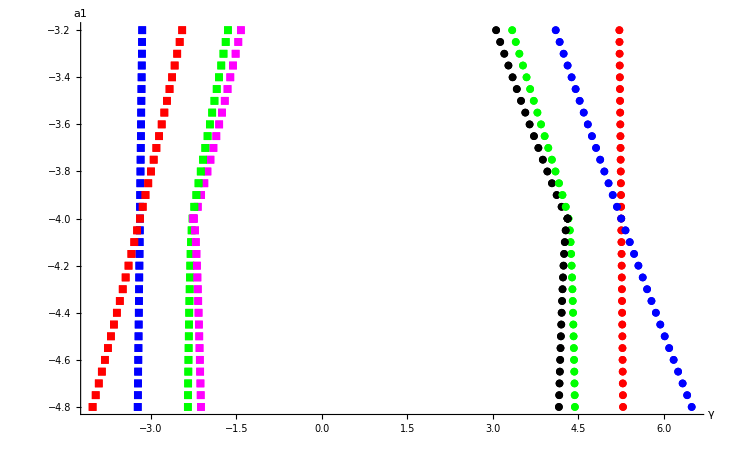

```mathematica
Show[Table[ListPlot[List/@points2[j,i],PlotStyle->colors[j,i],PlotMarkers->shapes[j,i]],{i,1,Length@ktbl},{j,1,Length@atbl}],PlotRange->{{-5,8},{-3,-5}},AxesLabel->{"γ","a1"},LabelStyle->Directive[Bold, Medium]]
```

```mathematica
Legended[Show[Table[ListPointPlot3D[List/@points[j,i],PlotStyle->colors[j,i](*,PlotMarkers->shapes[j,i]*)],{i,1,Length@ktbl},{j,1,Length@atbl}],PlotRange->All],Placed[PointLegend[{Black,Red,Blue,Magenta,Black},{"(00)created","(10)created","(01)created","(11)created","saddle created"}],{.93,0.8}]]
```

```mathematica
Clear[k12]
```

```mathematica
k12=1;
```

```mathematica
vec1[θ1_, θ2_, d_] := FullSimplify[D[Energy[θ1,θ2, d], 
     {{θ1,θ2}}]]; 
vc1[d_?NumericQ]:=θ1/. NSolve[vec1[θ1,θ2, d]==0,{θ1,θ2},Reals];
vc2[d_?NumericQ]:=θ2/. NSolve[vec1[θ1,θ2, d]==0,{θ1,θ2},Reals];
spliceThread=Splice@*Thread;
coords1=Table[spliceThread[{vc1[d],vc2[d],d}],{d,-12,12,.02}];
coords={#[[1]],#[[2]]}&/@coords1;
hessian=(D[Energy[x22,x33, y], {{x22,x33}},{{x22,x33}}]/.{x22->#[[1]],x33->#[[2]]})&/@coords;
eigenvals=Table[Eigenvalues[hessian[[i]]],{i,1,Length@hessian,1}];
vertexColors1=Which[#[[1]]>0&&#[[2]]>0,RGBColor[.94,.31,.22],#[[1]]>0&&#[[2]]<0,Magenta,#[[1]]<0&&#[[2]]>0,Magenta,#[[1]]<0&&#[[2]]<0,RGBColor[.122,.267,.62],Chop[#[[1]]]==0||Chop[#[[2]]]==0,Yellow]&/@eigenvals;
```

```mathematica
Show[ContourPlot3D[z==bifurcationpoints[[3,3]]+.1,{x,-2,2},{y,-2,2},{z,-10,10}],(*ContourPlot3D[{x==θ1m,y==θ1m,x==θ1p,y==θ2p},{x,-2,2},{y,-2,2},{z,-15,15}],*)ListPointPlot3D[List/@coords1,PlotStyle->vertexColors1],AxesLabel->{"θ1","θ2","γ"},LabelStyle->Directive[Bold, Medium],PlotRange->All]
```